```mathematica
g[x_]:=Sin[x]/x
```

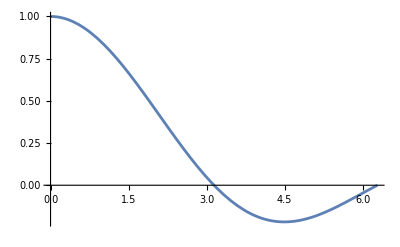

```mathematica
Plot[g[x],{x,0,2*Pi}]
```

```mathematica
g[1]
```

Sin[1]

```mathematica
N[g[1]]
```

0.841471

```mathematica
N[g[1.]]
```

0.841471

```mathematica
g@1
```

Sin[1]

```mathematica
1//g
```

Sin[1]

f (x) = | x |

```mathematica
mod[x_]:=If[x<0,-x,x]
```

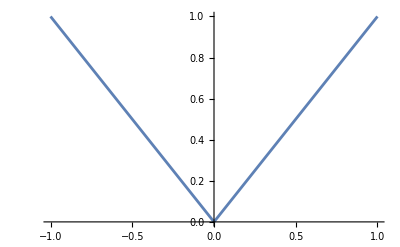

```mathematica
Plot[mod[x],{x,-1,1}]
```

中缀运算符

```mathematica
distance[x1_,x2_]:=Abs[x2-x1]
```

```mathematica
5~distance~10
```

5

```mathematica
list1={"apple","banana"};
list2={"cherry","date"};
```

```mathematica
list1~Join~list2
```

{apple,banana,cherry,date}

Apply @@

https://reference.wolfram.com/language/ref/Apply.html
Apply和@@可以去掉两层列表，@可以去掉一层列表

```mathematica
Apply[f,{a,b,c,d}]
```

f[a,b,c,d]

```mathematica
f@@{a,b,c,d}
```

f[a,b,c,d]

```mathematica
f@{a,b,c,d}
```

f[{a,b,c,d}]

Derivative

https://reference.wolfram.com/language/ref/Derivative.html

```mathematica
D[x^2,x]
```

2 x

```mathematica
d = D[x^3, x]
```

3 x^2

```mathematica
fd1[x_]=d (*不同于:=，没有:*)
```

3 x^2

```mathematica
fd2[x_]:=Evaluate[d]
```

```mathematica
fd2[1]
```

3

```mathematica
D[x^2*Cos[y^3],x,x] (*偏导*)
```

2 Cos[y^3]

```mathematica
D[x^2*Cos[z],{x,2},{z,5}]
```

-2 Sin[z]

```mathematica
d=D[x^3,x]
```

3 x^2

```mathematica
fd3[t_]:=d/.x-> t
```

```mathematica
Print[fd3[t]]
```

3 t^2

```mathematica
Derivative[1]
```

```mathematica
d1 = Derivative[2][Cos]
```

-Cos[#1]&

```mathematica
d1[Pi/6]
```

-(√3)/2

```mathematica
K[x_,y_]:=x^2+y^3
```

```mathematica
Derivative[1,2][K][u,v]
```

0

```mathematica
f[x_,y_]:=Cos[x] Sin[y]
Derivative[2,3][f][u,v]
```

-Sin[u] Sin[v]

Integrate

https://reference.wolfram.com/language/ref/Integrate.html

```mathematica
Integrate[x^2,x]
```

x^3/3

```mathematica
Integrate[x^2,x,x]
```

x^4/12

```mathematica
Integrate[x*Sin[y],x,y,x]
```

-1/6 x^3 Cos[y]

```mathematica
Integrate[x^2,{x,0,1}]
```

1/3

```mathematica
Integrate[Sin[x]/x,{x,0,Infinity}]
```

π/2

```mathematica
Integrate[Exp[Sin[x]],x]
```

∫ⅇ^Sin[x]ⅆx

```mathematica
Integrate[Exp[Sin[x]],{x,0,1}]
```

∫_0^1 ⅇ^Sin[x]ⅆx

```mathematica
NIntegrate[Exp[Sin[x]],{x,0,1}]
```

1.63187

Limit

https://reference.wolfram.com/language/ref/Limit.html

```mathematica
Limit[Sin[a*x]/Sin[b*x],x->0]
```

a/b

```mathematica
Limit[(Log[a,x+h]-Log[a,x])/h,h->0]
```

1/(x Log[a])

Series

https://reference.wolfram.com/language/ref/Series.html?q=Series

```mathematica
Series[Sin[x],{x,0,5}]
```

x-x^3/6+x^5/120+O[x]^6

list

```mathematica
l = {1,"abc",Log}
Length@l
```

{1,abc,Log}

3

```mathematica
l[[1]]
```

1

```mathematica
l[[0]]
```

List

```mathematica
l1 = {1,a,{3,12},Exp}
```

{1,a,{3,12},Exp}

```mathematica
l1[[3]]
```

{3,12}

```mathematica
l1[[3]][[2]]
```

12

```mathematica
l1[[3,2]]
```

12

```mathematica
l1[[2]]="text"
```

text

```mathematica
l1
```

{1,text,{3,12},Exp}

Insert

https://reference.wolfram.com/language/ref/Insert.html?q=Insert

```mathematica
l2 = Insert[l1,"new str",2]
```

{1,new str,text,{3,12},Exp}

Delete

https://reference.wolfram.com/language/ref/Delete.html?q=Delete

```mathematica
Delete[l1,1]
```

{text,{3,12},Exp}

Append

https://reference.wolfram.com/language/ref/Append.html?q=Append

```mathematica
l3 = {1,2,3}
```

{1,2,3}

```mathematica
Append[l3,4]
```

{1,2,3,4}

```mathematica
l3
```

{1,2,3}

```mathematica
AppendTo[l3,4]
```

{1,2,3,4}

```mathematica
l3
```

{1,2,3,4}

```mathematica
l4 = {1,2,3,4,5,6,7}
```

{1,2,3,4,5,6,7}

Span

https://reference.wolfram.com/language/ref/Span.html

```mathematica
l4[[2;;6;;2]]
```

{2,4,6}

```mathematica
l4[[2;; ;;2]]
```

{2,4,6}

```mathematica
l5 = {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15}
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15}

```mathematica
l5[[1;; ;;4]]
```

{1,5,9,13}